# Homework 3

## Problem 3.1

If someone were to drop two iron spheres, on of mass 1 kg and one of mass 10 kg from the leaning tower of Pisa, which would hit the ground first?  Assume constant acceleration, but include linear and quadratic drag. The height of the tower is 58.36 m to the top, so assume that the distance each ball falls before striking the ground is 55.0 m. The density of iron is 7860 kg / m^3. (Galileo stated that he didn't remember if he had tried the experiment or not, but others had tried it. Some stated that the time it took an object to fall was linearly proportional to its weight!)

```mathematica
Quit[]
```

```mathematica
h=55.0;
g=9.80;
m1=1;
m2=10;
rho=7860;
```

## Part A

Find the diameter of each ball.  Call these d1 and d2.

```mathematica
d1=2*(3*m1 /(4 * Pi * rho))^(1/3)
d2=2*(3*m2 /(4 * Pi * rho))^(1/3)
```

1/(1310 π)^(1/3)

1/(131 π)^(1/3)

### Hints

Remember that density=mass/volume
Volume of a sphere =4πr^3/3

### Solutions

```mathematica
vol1$=m1/rho;
d1$=N[2*((3*vol1$)/(4*Pi))^(1/3)];
r1$=0.5*d1$;
vol2$=m2/rho;
d2$=N[2*((3*vol2$)/(4*Pi))^(1/3)];
r2$=0.5*d1$;
err1$=Abs[d1-d1$]/d1$;
err2$=Abs[d2-d2$]/d2$;
If[err1$<.01,Print["d1 is correct"],Print["d1 is incorrect"]]
If[err2$<.01,Print["d2 is correct"],Print["d2 is incorrect"]]
err1$=Abs[(d1-d1$/2)]/(d1$/2);
err2$=Abs[(d2-d2$/2)]/(d2$/2);
If[err1$<.01,Print["You calculated a radius rather than a diameter for d1"]]
If[err2$<.01,Print["You calculated a radius rather than a diameter for d2"]]
```

d1 is correct

d2 is correct

## Part B

Write the equation of motion for each ball. Take x to be positive in the upward direction. When considering the signs to use for the linear and quadratic drag terms, note that that x’(t) will be negative for downward motion, but (x'(t))^2 will always be positive. This will influence what sign you put in front of each term.

You may write the derivatives either as x1'' [ t ] or D[ x1[ t ], {t,2} ], etc., but be sure to include the [ t ] notation.

```mathematica
beta=1.6*10^(-4);
gamma=.25;
eq1=m1*x1''[t]==-m1*g+-beta*d1 *x1'[t] +gamma*d1^2*(x1'[t])^2;
eq2=m2*x2''[t]==-m2*g+-beta*d2*x2'[t] + gamma * d2^2 * (x2'[t])^2;
```

### Solution

```mathematica
eq1$=m1*D[x1[t],{t,2}]==-m1*g-beta*d1*x1'[t]+gamma*d1^2*(x1'[t])^2;
eq2$=m2*x2''[t]==-m2*g-beta*d2*x2'[t]+gamma*d2^2*(x2'[t])^2;
a1A$=x1''[t]/.Solve[eq1$,x1''[t]][[1]];
a1B$=x1''[t]/.Solve[eq1,x1''[t]][[1]];
a2A$=x2''[t]/.Solve[eq2$,x2''[t]][[1]];
a2B$=x2''[t]/.Solve[eq2,x2''[t]][[1]];
If[FullSimplify[Solve[(a1A$/.x1'[t]->Dx1)==(a1B$/.x1'[t]->Dx1),Dx1]]=={{}},Print["Equation 1 is correct."],Print["Equation 1 is incorrect"]]
If[FullSimplify[Solve[(a2A$/.x2'[t]->Dx2)==(a2B$/.x2'[t]->Dx2),Dx2]]=={{}},Print["Equation 2 is correct."],Print["Equation 2 is incorrect"]]
```

Equation 1 is correct.

Equation 2 is correct.

## Part C

Solve these equations numerically, and find the approximate time it takes each ball to fall 55.0 m  by graphical analysis. 
Answers within 1% are considered correct.  
Adjust the plotting ranges until you are able to determine fairly accurately the time it takes to reach the ground.

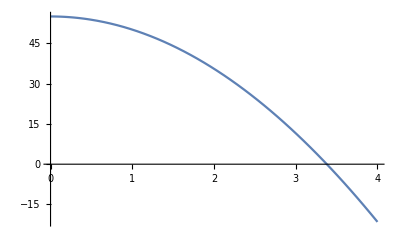

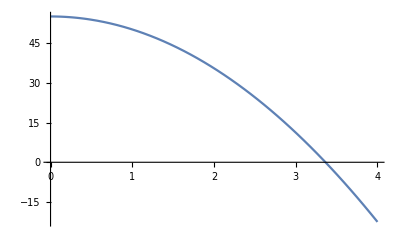

```mathematica
sol1=NDSolve[{eq1,x1[0]==55,x1'[0]==0},x1,{t,0,4}];
Plot[x1[t]/.sol1,{t,0, 4}]
sol2=NDSolve[{eq2,x2[0]==55,x2'[0]==0},x2,{t,0,4}];
Plot[x2[t]/.sol2,{t,0, 4}]
```

```mathematica
t1=3.4;
t2=3.38;
```

### Solutions

```mathematica
t1$=3.380;
t2$=3.364;
err1$=Abs[t1-t1$]/t1$;
err2$=Abs[t2-t2$]/t2$;
If[err1$<.01,Print["t1 is correct"],Print["t1 is not correct"]];
If[err2$<.01,Print["t2 is correct"],Print["t2 is not correct"]];
```

t1 is correct

t2 is correct

## Problem 3.2

You kick a smooth, spherical rock off a cliff. The diameter of the rock is 10.0 cm and the mass of the rock is 7.00 kg. The rock is travelling horizontally at a speed of 30 m/s as it reaches the edge of the cliff. After 3.24 seconds, you hear the rock strike something. How far did the rock fall? What is the horizontal component of its velocity as it strikes the ground below? Include both linear and quadratic drag in your calculation and assume the speed of sound is 330 m/s.

```mathematica
Quit[]
```

```mathematica
m=7.0;
g=9.81;
d=.10;
v0=30;
vs=330;
```

(A) Write an equation of motion for the X and Y directions.Take X to be positive in the direction of the initial horizontal kick and Y to be positive in the upward direction.

```mathematica
beta=1.6*10^-4;
gamma=.25;
eqx=m*x''[t]==-beta * d * x'[t] - gamma * d^2*((x'[t])^2 + (y'[t])^2)^(1/2) * x'[t]
eqy=m*y''[t]==-m*g -beta*d*y'[t] - gamma * d^2*((x'[t])^2 + (y'[t])^2)^(1/2) * y'[t]
```

7. x''[t]==-0.000016 x'[t]-0.0025 x'[t] √(x'[t]^2+y'[t]^2)

7. y''[t]==-68.67-0.000016 y'[t]-0.0025 y'[t] √(x'[t]^2+y'[t]^2)

### Solution

```mathematica
eqx$=m*x''[t]==-beta*d*x'[t]-gamma*d^2*√(x'[t]^2+y'[t]^2)*x'[t];
eqy$=m*y''[t]==-m*g-beta*d*y'[t]-gamma*d^2*√(x'[t]^2+y'[t]^2)*y'[t];
a1A$=x''[t]/.Solve[eqx$,x''[t]][[1]];
a1B$=x''[t]/.Solve[eqx,x''[t]][[1]];
a2A$=y''[t]/.Solve[eqy$,y''[t]][[1]];
a2B$=y''[t]/.Solve[eqy,y''[t]][[1]];
If[FullSimplify[Solve[(a1A$/.x'[t]->Dx)==(a1B$/.x'[t]->Dx),Dx]]=={{}},Print["x equation is correct."],Print["x equation is incorrect"]]
If[FullSimplify[Solve[(a2A$/.y'[t]->Dy)==(a2B$/.y'[t]->Dy),Dy]]=={{}},Print["y equation is correct."],Print["y equation is incorrect"]]
eqx$=m*x''[t]==-beta*d*x'[t]+gamma*d^2*√(x'[t]^2+y'[t]^2)*x'[t];
eqy$=m*y''[t]==-m*g-beta*d*y'[t]+gamma*d^2*√(x'[t]^2+y'[t]^2)*y'[t];
a1A$=x''[t]/.Solve[eqx$,x''[t]][[1]];
a1B$=x''[t]/.Solve[eqx,x''[t]][[1]];
a2A$=y''[t]/.Solve[eqy$,y''[t]][[1]];
a2B$=y''[t]/.Solve[eqy,y''[t]][[1]];
If[FullSimplify[Solve[(a1A$/.x'[t]->Dx)==(a1B$/.x'[t]->Dx),Dx]]=={{}},Print["Check the sign of your quadratic drag."]]
If[FullSimplify[Solve[(a2A$/.y'[t]->Dy)==(a2B$/.y'[t]->Dy),Dy]]=={{}},Print["Check the sign of your quadratic drag."]]
```

x equation is correct.

y equation is correct.

## Part B

Solve these equations simultaneously, subject to correct initial conditions.

First, use a fairly large range to be sure your solution has a correct behavior.

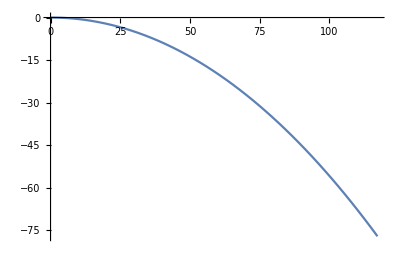

```mathematica
sol1=NDSolve[{eqx,eqy,x[0]==0,y[0]==0,x'[0]==v0,y'[0]==0},{x,y},{t,0,4}];
ParametricPlot[{x[t],y[t]}/.sol1,{t,0,4}]
```

Next, we want to calculate the time for the sound to come back to you plus the time the rock took to fall (call this T) as a function of the time the rock was falling (t). Use the symbols X and Y to represent the x and y coordinates of the landing position, respectively. Find an expression for T.

```mathematica
T=Sqrt[X^2 + Y^2] /vs + t
```

t+1/330 √(X^2+Y^2)

### Solution

```mathematica
T$=Sqrt[X^2+Y^2]/vs+t;
If[FullSimplify[Solve[T==T$,t]]=={{}},Print["T is correct."],Print["T is incorrect."]]
```

T is correct.

To determine t from the known value of T, we want to graph T(t) and see where it equals 3.24 s. First, we have to replace X and Y with the solutions from the differential equation. I’ll do this for you.

```mathematica
T=T/.{(X^2+Y^2)->({x[t]^2+y[t]^2}/.sol1)}
```

{{t+1/330 √((InterpolatingFunction[…][t])^2+(InterpolatingFunction[…][t])^2)}}

Now we can plot T(t). Adjust the time window in the plot below until you find a total time of 3.24 s, then read t from the graph.

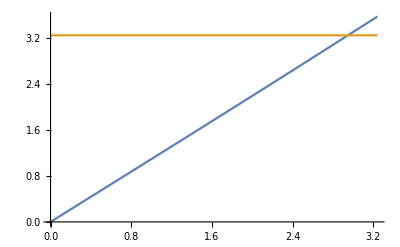

```mathematica
Plot[{T,3.24},{t,0, 3.24}]
```

Now find the y position and the x component of velocity at time t, again by selecting a time window that will let you determine the values fairly accurately.

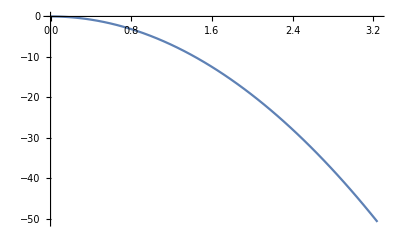

```mathematica
Plot[y[t]/.sol1,{t,0, 3.24}]
```

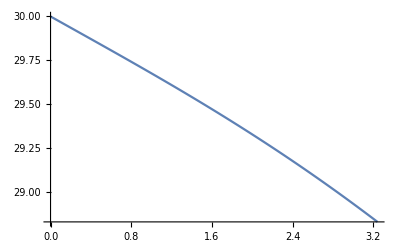

```mathematica
Plot[x'[t]/.sol1,{t,0, 3.24}]
```

```mathematica
yf=42;
vxf=28.9;
```

### Solution

```mathematica
yf$=42.14;
err1=Abs[Abs[yf]-yf$]/yf$;
If[err1<.01,Print["yf is correct."],Print["yf is not correct."]]
vxf$=28.956;
err2=Abs[Abs[vxf]-vxf]/vxf;
If[err2<.01,Print["vxf is correct."],Print["vxf is not correct."]]
```

yf is correct.

vxf is correct.

## Paper Problems

-Graphics-

-Graphics-

-Graphics-